# Action Items - GoL

## Developer

For Developer

### Create animation. Cut off gliders, etc. (DONE?)

SW did this

Here’s a typical example of what it looks like to run the Game of Life:

Create animation analogous to https://conwaylife.com/wiki/R-pentomino
Cut off gliders
Make the length 1103 case; possibly minimize cuboids

```mathematica
frames = 
Table[
ArrayPlot[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}}, 0}, {{{i}}, {-25, 35}, {-45, 45}}], Mesh->True,MeshStyle->Opacity[.1]], {i, 500}];
```

```mathematica
Export["anim2.mp4", frames]
```

### videos to add

Both should be stored in the cloud (under blog announcements) and available publicly

Blinker

```mathematica
AnimationVideo[(ArrayPlot[ArrayPad[#,{1,1}],Mesh->True,MeshStyle->Opacity[.2],ImageSize->200]&/@CellularAutomaton["GameOfLife",{$LifeData["Blinker"]["MatrixData"],0},24])[[i]], {i, 1, 24, 1}]
```

Glider

```mathematica
AnimationVideo[(ArrayPlot[ArrayPad[#,{1,1}],Mesh->True,MeshStyle->Opacity[.2],ImageSize->200]&/@CellularAutomaton["GameOfLife",{$LifeData["Glider"]["MatrixData"],0},48])[[i]], {i, 1, 48, 1}]
```

AnimationVideo::prpchg: Warning: the output frame rate changed from 48/5 to 9598367/1000000.

### Show only center region etc.

I’ve always found it difficult to get a good sense of what’s going in a 2D cellular automaton by looking at a video.  With a class 4 rule like the Game of Life it often helps to have still frames that include “trails” of what’s happened before, and we’ll often use that type of visualization in what follows:

Show only center region etc.
Possibly do a stack of two rows

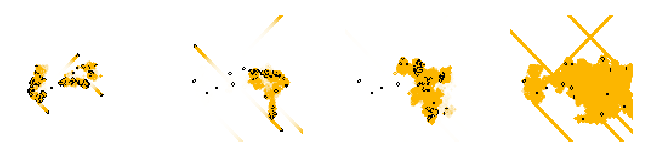

```mathematica
GraphicsRow[CellularAutomatonHistoryPlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{#,{-50,50},{-50,50}},Mesh->(#<100),"Decay"-><|150->.9,300->.95,600->.98,1200->.999|>[#]]&/@{150,300,600,1200}]
```

Showing only the center region looks bad because you can’t see the gliders.

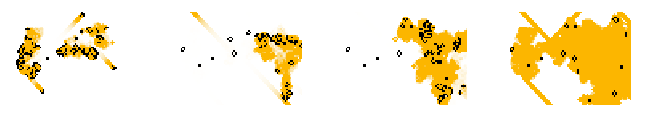

```mathematica
GraphicsRow[CellularAutomatonHistoryPlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{#,{-20,35},{-40,35}},Mesh->(#<100),"Decay"-><|150->.9,300->.95,600->.98,1200->.999|>[#], ImageSize-> {Automatic, 200}]&/@{150,300,600,1200}]
```

We can try different zoom levels:

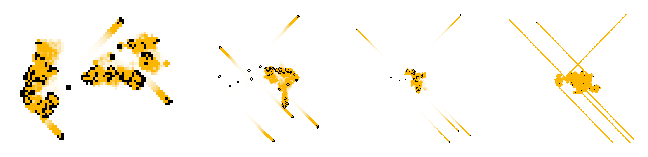

```mathematica
GraphicsRow[CellularAutomatonHistoryPlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},If[# ==1200, {#,{-150,150},{-150,150}}, #],Mesh->(#<100),"Decay"-><|150->.9,300->.95,600->.98,1200->.999|>[#], ImageSize-> {Automatic, 200}]&/@{150,300,600,1200}]
```

Or stacking:

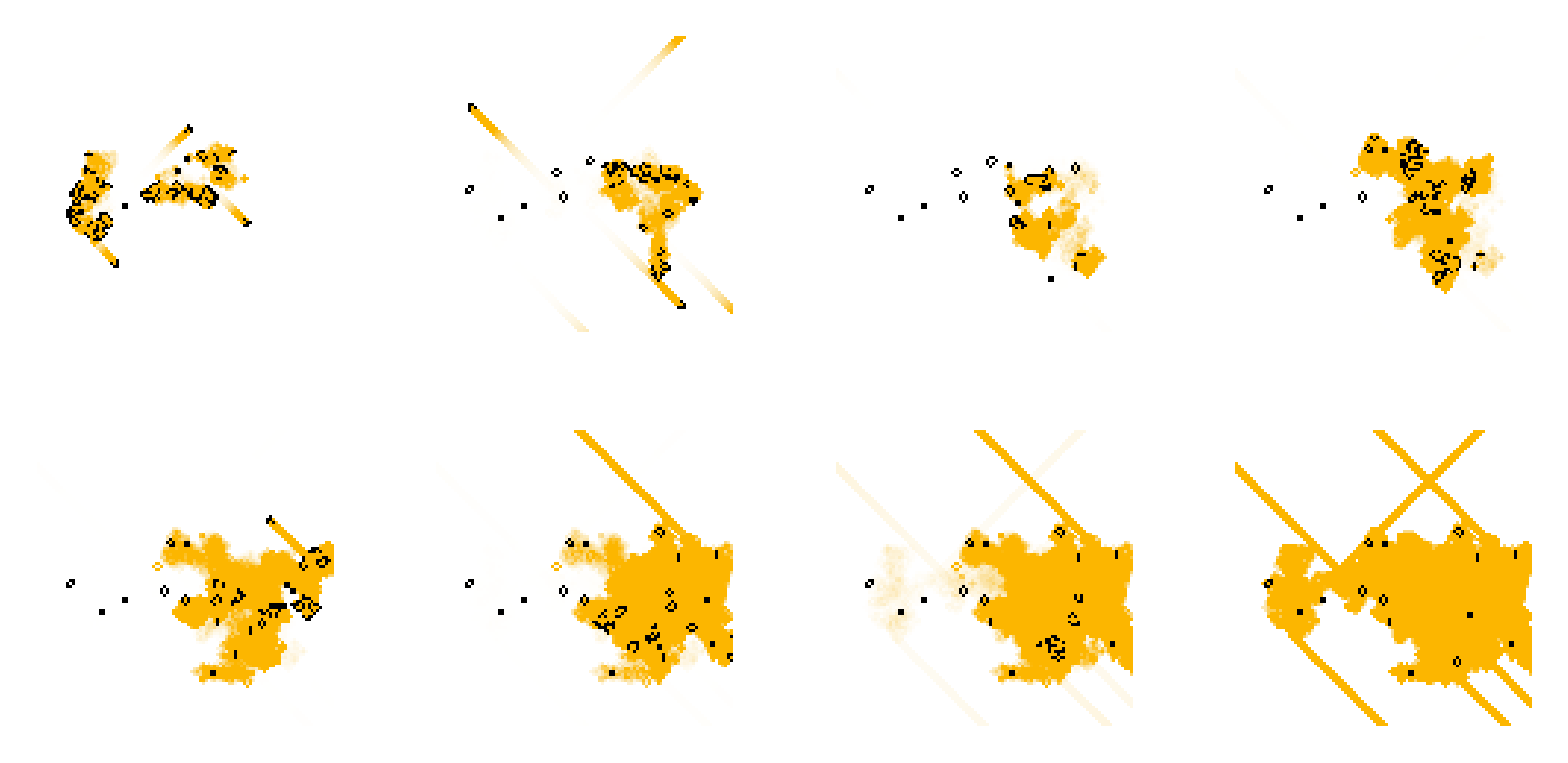

```mathematica
GraphicsGrid[Partition[CellularAutomatonHistoryPlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{#,{-50,50},{-50,50}},Mesh->(#<100),"Decay"-><|150->.9,300->.95,450-> .95, 600->.98,750->.985,900->.99,1050-> .995,  1200->.999|>[#]]&/@{150,300,450,600,750,900,1050,1200}, 4]]
```

### Perhaps use E heptomino. Possibly try to get full 1103 step case

To get a more global view of what’s going on it’s sometimes useful to look at the whole (2+1)-dimensional “spacetime history”:

Perhaps use E heptomino instead: {{0, 1, 1, 1}, {1, 1, 0, 0}, {0, 1, 1, 0}}
Possibly try to get full 1103 step case

```mathematica
GraphicsRow[CellularAutomatonPlot3D["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},#]&/@{150,300}]
```

-Graphics-

E heptomino

```mathematica
GraphicsRow[CellularAutomatonPlot3D["GameOfLife",{{{0,1,1,1},{1,1,0,0},{0,1,1,0}},0},#]&/@{150,300}]
```

-Graphics-

1103

```mathematica
CellularAutomatonPlot3D["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{1103, {-50, 50}, {-50, 50}}]
```

-Graphics3D-

Splitting and showing as a row:

```mathematica
GraphicsRow[CellularAutomatonPlot3D["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{#, {-50, 50}, {-50, 50}}]&/@ {{0, 275}, {276, 551}, {552, 827}, {828, 1103}}]
```

-Graphics-

### Investigate slices to take. Could be complete silhouettes

Taking a slice through this to form “silhouettes” we get pictures that look remarkably similar to what I generated starting in the early 1980s from 1D cellular automata:

Investigate slices to take  
Or could be complete silhouettes

```mathematica
GraphicsRow[CellularAutomatonSpacetimePlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},#,"Decay"->.99,Mesh->(#<200)]&/@{150,300,600,900}]
```

-Graphics-

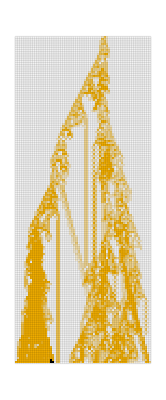

```mathematica
GraphicsRow[CellularAutomatonSpacetimePlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},#,"Decay"->.95,Mesh->(#<200)]&/@{150}]
```

Silhouette:

```mathematica
GraphicsRow[CellularAutomatonSpacetimePlot["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},#,"Decay"->1,Mesh->(#<200)]&/@{900}]
```

-Graphics-

### Flip so all go to the right

Here are a few small examples of such “spaceship”-style structures:

Flip so all go to the right

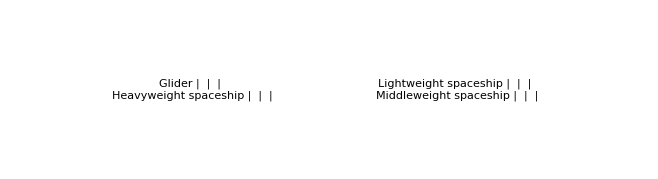

```mathematica
GraphicsRow[Grid[CellularAutomatonCompositePlot[#,{"Static"->{60, 60},{"Trails",20,.9}->{100, 60},{"3D",8}->{60, 60}},1, "Transform"-> If[# === "Glider", Identity, (Reverse/@#&)]]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{1}, 2.5}]&/@Partition[{"Glider","Heavyweight spaceship","Lightweight spaceship","Middleweight spaceship"},2],Spacings->30]
```

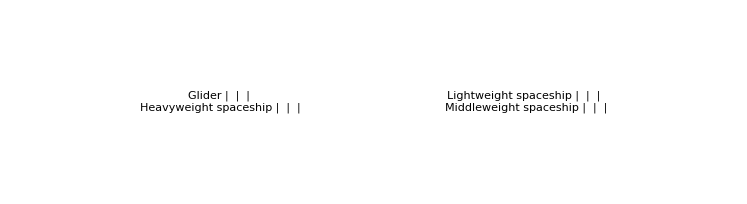

```mathematica
GraphicsRow[Grid[CellularAutomatonCompositePlot[#,{"Static"->{60, 60},{"Trails",20,.9}->{100, 60},{"3D",8}->{60, 60}},"Margin"-> 1, "Transform"-> If[# === "Glider", Identity, (Reverse/@#&)]]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{1}, 2.5}]&/@Partition[{"Glider","Heavyweight spaceship","Lightweight spaceship","Middleweight spaceship"},2],Spacings->30]
```

### Need to update these guys as well (image is the same but code is different)

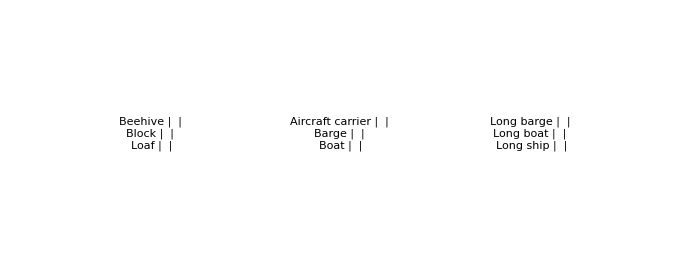

```mathematica
GraphicsRow[Grid[CellularAutomatonCompositePlot[#,{{"Trails",10,.9}->{Automatic, 60},{"3D",6}->{60, 60}}]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{2->1, 2.5}]&/@ Partition[{"Beehive","Block","Loaf","Aircraft carrier","Barge","Boat","Long barge","Long boat","Long ship"},3], Spacings->{38, Automatic}]
```

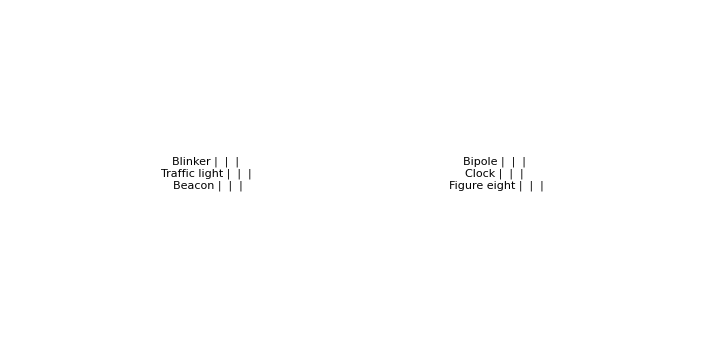

```mathematica
GraphicsRow[Grid[CellularAutomatonCompositePlot[#,{"Static"->{60, 60},{"Trails",10,.9}->{60, 60},{"3D",6}->{60, 60}}]&/@#,Dividers->{False,All},FrameStyle->Opacity[.3 ], Spacings->{{1}, 2.5}]&/@Partition[{"Blinker","Traffic light","Beacon","Bipole","Clock","Figure eight","Figure eight"},3],Spacings->30]
```

### Fix cell sizes. Line up etc. (DONE?)

Still lifes, oscillators and spaceships are most of what one sees in the “ash” that survives from typical random initial conditions.  And for example the end result (after 1103 steps) from the evolution we saw in the previous section consists of:

Fix cell sizes
Line up etc.
Should say 8×   etc.
Align by numbers at the top

```mathematica
GraphicsGrid[With[{ca=PatternElements[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{{{1104}}}]]},{KeyValueMap[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#,0},8,ImageSize->50],Text[StringJoin[ToString[#2],"×"]],Top]&,ca],KeyValueMap[CellularAutomatonPlot3D["GameOfLife",{#,0},14,ImageSize->{Automatic,100}]&,ca]}]]
```

-Graphics-

```mathematica
Grid[With[{ca=PatternElements[CellularAutomaton["GameOfLife",{{{0,1,1},{1,1,0},{0,1,0}},0},{{{1104}}}]]},{KeyValueMap[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#,0},8,ImageSize->50],Text[StringJoin[ToString[#2],"×"]],Top]&,ca],KeyValueMap[CellularAutomatonPlot3D["GameOfLife",{#,0},14,ImageSize->{Automatic,100}]&,ca]}], Alignment->Top, Dividers->{All, False},FrameStyle->Opacity[.3], Spacings->{2.4,Automatic}]
```

-Graphics-8× | -Graphics-4× | -Graphics-4× | -Graphics-3× | -Graphics-1× | -Graphics-3× | -Graphics-1× | -Graphics-1×
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

### Have this loop at correct number of frames (DONE?)

The structures we’ve seen so far were all found quickly after the Game of Life was invented; indeed, pretty much as soon it was simulated on a computer.  But one feature that they all share is that they don’t systematically grow; they always return to the same number of black cells.  And so one of the early surprises (in 1970) was the discovery of a “glider gun” that shoots out a glider every 30 steps forever:

Have this loop at correct number of frames

```mathematica
AnimationVideo[ArrayPlot[CellularAutomaton["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0}, {{{i}}, {-5, 35}, {-5, 45}}], Mesh->True,MeshStyle->Opacity[.05],ImageSize->250], {i, 1, 200, 1}]
```

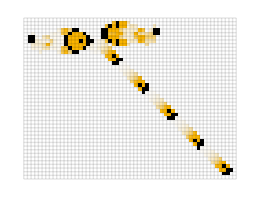
-Graphics--Graphics3D--Graphics-

```mathematica
Row[{CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0},150,ImageSize->260],CellularAutomatonPlot3D["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0},100,ImageSize->140,ViewPoint->{-2.198487002413733,-2.3413385931086927,1.0652645176845457}],CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0},250,"Decay"->.99,ImageSize->95,Mesh->None]},Spacer[30]]
```

```mathematica
vid = AnimationVideo[ArrayPlot[CellularAutomaton["GameOfLife",{$LifeData["Gosper glider gun"]["MatrixData"], 0}, {{{i}}, {-5, 35}, {-5, 45}}], Mesh->True,MeshStyle->Opacity[.05],ImageSize->250], {i, 101, 131, 1}];
```

AnimationVideo::prpchg: Warning: the output frame rate changed from 31/5 to 3100241/500000.

```mathematica
loopedVideo=VideoJoin[Table[vid, 3]];
```

```mathematica
loopedVideo
```

This kind of works but if fs up the quality

### Spacing needs to be fixed

Something that gives a sense of progress that’s been made in Game-of-Life “technology” is that a “more efficient” glider gun---with period 15---was discovered, but only in 2024, 54 years after the previous one:

Spacing needs to be fixed

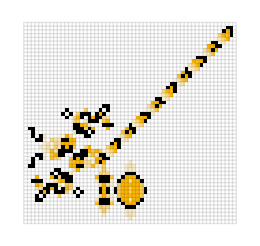
-Graphics--Graphics3D--Graphics-

```mathematica
Row[{CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Period-15 glider gun"]["MatrixData"], 0},150,ImageSize->260,"Decay"->.7],CellularAutomatonPlot3D["GameOfLife",{$LifeData["Period-15 glider gun"]["MatrixData"], 0},100,ImageSize->304,ViewPoint->{3.0373115164062576,-1.449486231706877,0.35175050305311767}],CellularAutomatonSpacetimePlot["GameOfLife",{$LifeData["Period-15 glider gun"]["MatrixData"], 0},250,"Decay"->.99,ImageSize->90,Mesh->None]},Spacer[0]]
```

I can’t figure what SW means by this.

### Put ticks underneath at particular numbers (with FrameTicks-> XXX)

So what other kinds of things can be built in the Game of Life?  Lots---even from the simple structures we’ve seen so far.  For example, here’s a pattern that was constructed to compute the primes

Put ticks underneath at particular numbers  (with FrameTicks-> XXX)
Use .95 for the decay

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{Import["https://www.conwaylife.com/patterns/primer.rle"],0},1600,Mesh->None,"Decay"->.97, FrameTicks->Automatic]
```

-Graphics-

```mathematica
r = Import["https://www.conwaylife.com/patterns/primer.rle"];
```

```mathematica
CellularAutomatonHistoryPlot["GameOfLife",{r,0},1600,Mesh->None,"Decay"->.97, FrameTicks->{False,Table[{60*Prime[i] - 115, Prime[i]}, {i, 1,6}]}]
```

-Graphics-

### Mark numbers here too

emitting a “lightweight spaceship” at step 100+120n only if n is prime.  It’s a little more obvious how this works when it’s viewed “in spacetime”; in effect it’s running a sieve in which all multiples of all numbers are instantiated as streams of gliders, which knock out spaceships generated at non-prime positions:

Mark numbers here too

```mathematica
CellularAutomatonSpacetimePlot["GameOfLife",{Import["https://www.conwaylife.com/patterns/primer.rle"],0},1600,Mesh->None,"Decay"->.99]
```

-Graphics-

Too long to run but this works

```mathematica
Show[CellularAutomatonSpacetimePlot["GameOfLife",{Import["https://www.conwaylife.com/patterns/primer.rle"],0},1600,Mesh->None,"Decay"->.99],FrameTicks->{Table[{60*Prime[i] - 115, Prime[i]}, {i, 1,5}], False, False, False}]
```

-Graphics-

### Get rid of space above and below

As we’ll see, often (but not always) these discoveries built on “new devices” and “new mechanisms” that were identified in the intervening years.  A long series of such “devices” and “mechanisms” involved handling “signals” associated with streams of gliders.  For example, the “glider pusher” (from 1993) has the somewhat subtle (but useful) effect of “pushing” a glider by one cell when it goes past:

Get rid of space above and below

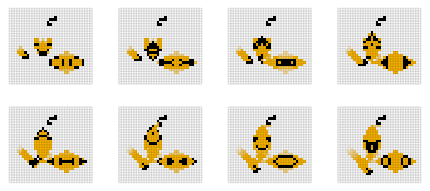
-Graphics--Graphics3D-

```mathematica
Row[{GraphicsGrid[Partition[Table[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Glider pusher"]["MatrixData"],0},{4 n,{-2,25},{-2,28}},"Decay"->.93],{n,2,9}],4]],CellularAutomatonPlot3D["GameOfLife",{$LifeData["Glider pusher"]["MatrixData"],0},40,ViewPoint->{2.088321875639556,-2.6284768080224388,0.42428930391120906},ImageSize->{Automatic,250}, PlotRangePadding->None]}]
```

```mathematica
GraphicsRow[{GraphicsGrid[Partition[Table[CellularAutomatonHistoryPlot["GameOfLife",{$LifeData["Glider pusher"]["MatrixData"],0},{4 n,{-2,25},{-2,28}},"Decay"->.93],{n,2,9}],4], ImageSize-> {Automatic, 200}],CellularAutomatonPlot3D["GameOfLife",{$LifeData["Glider pusher"]["MatrixData"],0},40,ViewPoint->{2.088321875639556,-2.6284768080224388,0.42428930391120906},ImageSize->{Automatic,200}, PlotRangePadding->None]}]
```

-Graphics-

### Fix spacing

We can see several waves of activity---and we can begin to get a sense of what happened by looking down at structures broken down by category:

[[[CAEngineering-01]]]
Fix spacing!!
Probably

```mathematica
discs=Sort/@Map[Map[Last],GroupBy[Transpose[Values/@{$LifeData[[All,"Class"]],$LifeData[[All,"Year"]]}],First]];
```

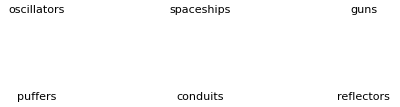

```mathematica
GraphicsGrid[Partition[KeyValueMap[Labeled[Histogram[#2,{1},PlotRange->{{1969,2025},Automatic},Frame->True,FrameTicks->{Automatic,None},AspectRatio->.3,PlotRangePadding->{Automatic,{0,Scaled[.15]}}],Text[ToLowerCase[Pluralize@#1]],Bottom]&,],3],Spacings->{-20,5}]
```

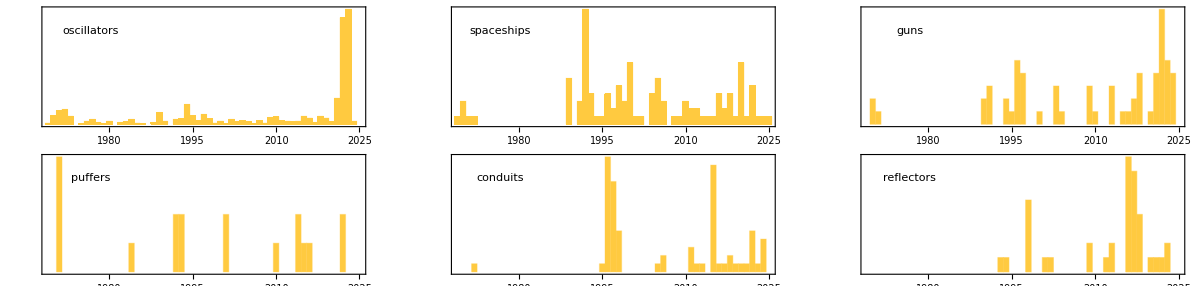

```mathematica
GraphicsGrid[Partition[KeyValueMap[Histogram[#2,{1},PlotRange->{{1969,2025},Automatic},Frame->True,FrameTicks->{Automatic,None},AspectRatio->.3,ImageSize->200,PlotRangePadding->{Automatic,{0,Scaled[.15]}},Epilog->Style[Text[ToLowerCase[Pluralize@#1],Scaled[{.15,.8}]],Small]]&,],3]]
```

### Make stacked version

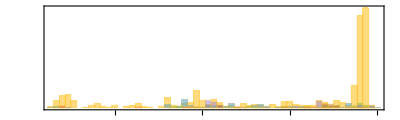

```mathematica
Histogram[
KeyValueMap[
Legended[#2,Text[ToLowerCase[Pluralize@#1]]]&,],{1},PlotRange->{{1969,2025},Automatic},Frame->True,FrameTicks->{Automatic,None},AspectRatio->.3,PlotRangePadding->{Automatic,{0,Scaled[.15]}}]
```

Make stacked version

For oscillators we see somewhat continuous activity, with rapid acceleration recently.  For “spaceships” and “guns” we see a long dry spell from the early 1970s until the 1990s.  And for conduits and reflectors we see little until sudden peaks of activity, in the mid-1990s and mid-2010s respectively.

### Make sure the yellow fills (DONE?)

So what is the dominant methodology?  Looking at descriptions of recently recorded structures, here’s a comparison XXXXXXMining descriptions of recently recorded structures, one finds 

 In recent

Make sure the yellow fills

```mathematica
fdata=Import["https://conwaylife.com/wiki/LifeWiki:News_archive","FullData"];
```

```mathematica
ydata=Discard[fdata[[4,5,7,1,5;;-1]],Flatten[#]==={}&];
```

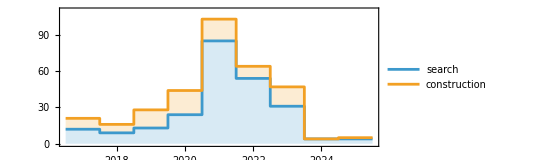

```mathematica
ListStepPlot[Reverse/@Transpose[Most[{Total@Sign@StringCount[#,"discover"|"use"],Total@Sign@StringCount[#,"construct"]}&/@ydata]],Center,PlotLayout->"Stacked",Filling->{2->{1},1->Axis},Frame->True,PlotRange->{{0.5,Automatic},{0,110}},PlotLegends->{"search","construction"},AspectRatio->.4,FrameTicks->{{Automatic,None},{Transpose[{Range[2,8],Riffle[Range[2018,2025,2],None]}],Automatic}}]
```

### Probably remove lines that don’t terminate within this plot

Probably remove lines that don’t terminate within this plot

```mathematica
Module[{osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&],firsts},firsts=Flatten[Values[mins/@GroupBy[osc,#Period&,Sort[#Year&/@#]&]]];ListPlot[KeyValueMap[If[MemberQ[firsts,#1],Callout[Style[{#2["Year"],#2["Period"]},PointSize[.01],Red],ArrayPlot[#2["MatrixData"],ImageSize->Tiny]],{#2["Year"],#2["Period"]}]&,osc],PlotRange->{{1968,1980},{0,30}},Frame->True,AspectRatio->.4,Epilog->({Opacity[.2],HalfLine[{#Year,#Period},{-1,0}]&/@Lookup[osc,firsts]})]]
```

-Graphics-

```mathematica
Module[{osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&],firsts},firsts=Flatten[Values[mins/@GroupBy[osc,#Period&,Sort[#Year&/@#]&]]];ListPlot[KeyValueMap[If[MemberQ[firsts,#1],Callout[Style[{#2["Year"],#2["Period"]},PointSize[.01],Red],ArrayPlot[#2["MatrixData"],ImageSize->Tiny]],{#2["Year"],#2["Period"]}]&,osc],PlotRange->{{1968,1980},{0,30}},Frame->True,AspectRatio->.4,Epilog->({Opacity[.2],HalfLine[{#Year,#Period},{-1,0}]&/@Select[Lookup[osc,firsts], #Year<1981&]})]]
```

-Graphics-

### Put callout on SMALLEST oscillator of a given period

Put callout on SMALLEST oscillator of a given period...   Perhaps indicate that with a larger blue dot

```mathematica
Module[{osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&],firsts},firsts=Flatten[Values[mins/@GroupBy[osc,#Period&,Sort[#Year&/@#]&]]];ListPlot[KeyValueMap[If[MemberQ[firsts,#1],Callout[Style[{#2["Year"],#2["Period"]},PointSize[.01],Red],ArrayPlot[#2["MatrixData"],ImageSize->Tiny]],{#2["Year"],#2["Period"]}]&,osc],PlotRange->{{0,25}},Frame->True,AspectRatio->.4,Epilog->({Opacity[.2],HalfLine[{#Year,#Period},{-1,0}]&/@Lookup[osc,firsts]})]]
```

-Graphics-

```mathematica
mins[assoc_]:=Keys[Select[assoc,#==Min[assoc]&]]
```

```mathematica
Module[{osc, firsts, smallest},osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&];
firsts=Flatten[Values[mins/@GroupBy[osc,#Period&,Sort[#Year&/@#]&]]];
smallest=Flatten[Values[mins/@GroupBy[osc,#Period&,Sort[Times@@Dimensions[#MatrixData]&/@#]&]]];
ListPlot[
KeyValueMap[
If[MemberQ[smallest,#1],
Callout[Style[{#2["Year"],#2["Period"]}, PointSize[.01]],ArrayPlot[#2["MatrixData"],ImageSize->Tiny]], If[MemberQ[firsts, #1], 
Style[{#2["Year"],#2["Period"]}, Directive[PointSize[.01],Red]],{#2["Year"],#2["Period"]}]
]&,osc],PlotRange->{{0,25}},Frame->True,AspectRatio->.4,Epilog->({Opacity[.2],HalfLine[{#Year,#Period},{-1,0}]&/@Lookup[osc,firsts]})]]
```

-Graphics-

### Show sequence of oscillator discoveries, with periods

```mathematica
Module[{osc=Select[Select[$LifeData,#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period<=100&],firsts},firsts=Flatten[Values[mins/@GroupBy[osc,#Period&,Sort[#Year&/@#]&]]];ListPlot[KeyValueMap[If[MemberQ[firsts,#1],Callout[Style[{#2["Year"],#2["Period"]},PointSize[.01],Red],ArrayPlot[#2["MatrixData"],ImageSize->Tiny]],{#2["Year"],#2["Period"]}]&,osc],PlotRange->{{0,25}},Frame->True,AspectRatio->.4,Epilog->({Opacity[.2],HalfLine[{#Year,#Period},{-1,0}]&/@Lookup[osc,firsts]})]]
```

-Graphics-

Show sequence of oscillator discoveries, with periods  ;;; perhaps double decker with smallest of that period underneath

I can’t figure what SW means by this.

### Show sequence of periods with discovery year

Show sequence of periods, with discovery year   doubledecker

I can’t figure what SW means by this.

[ Smaller (by bounding box) ]

### Make the numbers into callouts on the number lines

Make the numbers into callouts on the number lines
Use total number that balances columns best

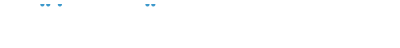
-Graphics-
-Graphics-period 2  
-Graphics-
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-
-Graphics-period 6  
-Graphics-
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-
-Graphics-period 10  
-Graphics-
-Graphics-period 11  
-Graphics-
-Graphics-period 12  -Graphics-
-Graphics-period 13  
-Graphics-
-Graphics-period 14  
-Graphics-
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-
-Graphics-period 17  
-Graphics-
-Graphics-period 18  
-Graphics-
-Graphics-period 19  
-Graphics-
-Graphics-period 20  
-Graphics-period 21

```mathematica
Row[Column[Table[
Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,ImageSize->3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[#Year],BaselinePosition->Top]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1969,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{Range[2,12],Range[13,21]},Spacer[15]]
```

```mathematica
ClearAll@place
place[currloc_, data_]:= 
Module[{size}, 
size = 2Last[Dimensions[First@CellularAutomaton["GameOfLife",{data["MatrixData"],0},data["Period"]]]];
Sow[Callout[{data["Year"] - 1969, 0}, 
Rotate[Labeled[CellularAutomatonHistoryPlot["GameOfLife", {data["MatrixData"], 0}, data["Period"], ImageSize->3.5size^(3/4),Mesh->True,MeshStyle->Opacity[.1]], data["Year"]], -90Degree], {currloc[[1]] ,10} ,LeaderSize->{{Automatic,90 °,3}, {3,90°}}
]];
{currloc[[1]] +2.25size^(1/1.5), currloc[[2]]}]
```

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[ListPlot[Reap[Fold[place,{3,1},SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]]][[2]], PlotRange->{{-10, 2025 - 1969+30}, {-10, 55}}, Axes->None, PlotStyle->PointSize[.03], ImageSize->{210, Automatic}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{Range[2,11],Range[12,21]},Spacer[15], Alignment->Top]
```

-Graphics-period 2  
-Graphics-period 3  
-Graphics-period 4  
-Graphics-period 5  
-Graphics-period 6  
-Graphics-period 7  
-Graphics-period 8  
-Graphics-period 9  
-Graphics-period 10  
-Graphics-period 11  -Graphics-period 12  
-Graphics-period 13  
-Graphics-period 14  
-Graphics-period 15  
-Graphics-period 16  
-Graphics-period 17  
-Graphics-period 18  
-Graphics-period 19  
-Graphics-period 20  
-Graphics-period 21